```mathematica
score[l_]:=Times@@Factorial/@Join[l,Tally[l][[All,2]]]
minimalPartitions[n_]:=MinimalBy[IntegerPartitions[n],score]
```

```mathematica
((score[#[[1]]])&/@(minimalPartitions/@Range[25]))//MatrixForm
```

(1
2
2
4
8
12
24
48
96
288
576
1152
2304
6912
13824
27648
82944
165888
497664
1327104
2985984
7962624
19906560
59719680
143327232)

```mathematica
wd
```

```mathematica
minimalPartitions[50]
```

{{6,5,5,4,4,4,3,3,3,3,2,2,2,2,1,1}}

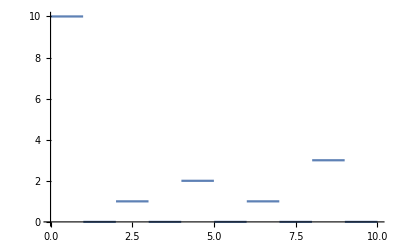

```mathematica
Plot[Sum[Floor[Cos[Pi Floor[x]/2^k]^2],{k,1,10}],{x,0,10}]
```

```mathematica
ci[k_,x_]:=Cos[Pi x/2^k]
cs[0,x_]:=ci[-1,x]
cs[n_,x_]:=(cs[n-1,x]+ci[n-2,x])/2
```

```mathematica
Sum[cs[i,x],{i,1,3}]//Expand
```

1/2 Cos[(π x)/2]+3/4 Cos[π x]+7/4 Cos[2 π x]

```mathematica
MatrixForm[{Cos[2Pi x],Cos[Pi x]/2+Cos[2 Pi x]/2,Cos[Pi x/2]/2+Cos[Pi x]/4+Cos[2 Pi x]/4}]
MatrixForm[{Cos[2Pi x],Cos[Pi x]/2+3Cos[2 Pi x]/2,Cos[Pi x/2]/2+3Cos[Pi x]/4+7Cos[2 Pi x]/4}]
```

(Cos[2 π x]
1/2 Cos[π x]+1/2 Cos[2 π x]
1/2 Cos[(π x)/2]+1/4 Cos[π x]+1/4 Cos[2 π x])

(Cos[2 π x]
1/2 Cos[π x]+3/2 Cos[2 π x]
1/2 Cos[(π x)/2]+3/4 Cos[π x]+7/4 Cos[2 π x])

```mathematica
Sum[2Cos[2Pi x/2^k],{k,0,10}]
```

2 Cos[(π x)/512]+2 Cos[(π x)/256]+2 Cos[(π x)/128]+2 Cos[(π x)/64]+2 Cos[(π x)/32]+2 Cos[(π x)/16]+2 Cos[(π x)/8]+2 Cos[(π x)/4]+2 Cos[(π x)/2]+2 Cos[π x]+2 Cos[2 π x]

```mathematica
Expand[c[x/2](1+c[x/4](1+c[x/8](1+c[x/16])))]
```

Cos[(π x)/2]^2+Cos[(π x)/4]^2 Cos[(π x)/2]^2+Cos[(π x)/8]^2 Cos[(π x)/4]^2 Cos[(π x)/2]^2+Cos[(π x)/16]^2 Cos[(π x)/8]^2 Cos[(π x)/4]^2 Cos[(π x)/2]^2

```mathematica
c[n_,x_]:=Sum[Product[Cos[Pi x/2^i]^2,{i,1,k}],{k,1,n}]
```

```mathematica
Sum[Product[Cos[Pi x/2^i]^2,{i,1,k}],{k,1,Infinity}]
```

∑_(k=1)^∞ ∏_(i=1)^k Cos[2^-i π x]^2

```mathematica
∑_(k=1)^30 ∏_(i=1)^k Cos[2^-i π #]^2&/@Range[25]
```

{0,1,0,2,0,1,0,3,0,1,0,2,0,1,0,4,0,1,0,2,0,1,0,3,0}

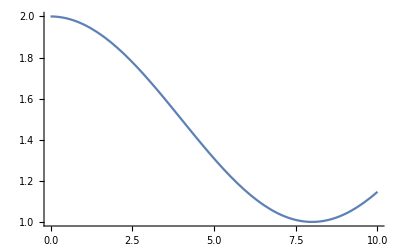

```mathematica
Plot[(1+c[x/16]),{x,0,10},PlotRange->Full]
```

```mathematica
cs[2,x]
```

1/2 (Cos[π x]+Cos[2 π x])

```mathematica
cs[3,x]//Expand
```

1/2 Cos[(π x)/2]+1/4 Cos[π x]+1/4 Cos[2 π x]

```mathematica
c[x_]:=Cos[Pi x]^2
evenSpike[0,x_]:=c[x];
evenSpike[k_,x_]:=evenSpike[k-1,x]c[x/2^k];
```